```mathematica
f[x_,a_]:=Exp[-x]x^a/Gamma[1+a,1]
```

```mathematica
μ[a_]=Integrate[x f[x,a],{x,1,∞}]
```

Gamma[2+a,1]/Gamma[1+a,1]

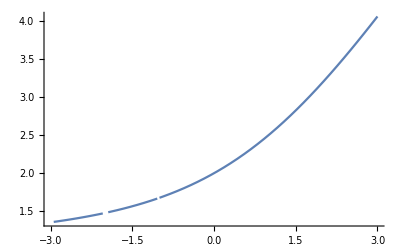

```mathematica
Plot[μ[a],{a,-3,3}]
```

```mathematica
Integrate[μ[a],{a,0,1}]
```

∫_0^1 Gamma[2+a,1]/Gamma[1+a,1]ⅆa